```mathematica
Clear[A,σ,x,ψ,m,ω,ℏ]
Refine[Integrate[1/(Sqrt[√π σ])^2 Exp[- x^2/σ^2],{x,-∞,+∞}]//Normal,{σ>0}]
```

1

```mathematica
Clear[A,σ,x,ψ,m,ω,ℏ,Hψ,Eψ]

m=1;
ℏ=1;
ω=1;
ψ=1/(Sqrt[√π σ]) Exp[-0.5 x^2/σ^2]
Hψ=-0.5D[ψ,{x,2}]+0.5 x^2 ψ//FullSimplify
Eψ=Refine[Integrate[ψ Hψ,{x,-∞,+∞}]//Normal,{σ>0}]//FullSimplify
```

(ⅇ^(-(0.5 x^2)/σ^2))/(π^(1/4) √σ)

(ⅇ^(-(0.5 x^2)/σ^2) (0.375563 σ^2+x^2 (-0.375563+0.375563 σ^4)))/σ^(9/2)

(0.25+0.25 σ^4)/σ^2

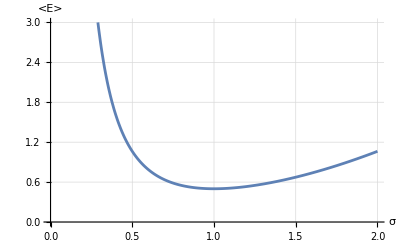

```mathematica
Plot[Eψ,{σ,0,2},AxesLabel->{"σ","<E>"},PlotRange->{0,3},GridLines->Automatic]
```

```mathematica
Solve[D[Eψ,σ]==0,σ,Reals][[2,1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

σ→1.

```mathematica
Eψ/.{σ->1}
```

0.5